```mathematica
nn=80001;
ll=50;
prec=120;
nData=10;
γ=1/2//N[#,prec]&;
λ=1/2//N[#,prec]&;
a0=λ//N[#,prec]&;
a1=(1-γ)/2//N[#,prec]&;
a2=(1+γ)/2//N[#,prec]&;
α[θ_]=(a0+ Cos[θ]);
β[θ_]=(-a1+a2) Sin[θ];
ω[θ_]=Sqrt[α[θ]^2+β[θ]^2];
ϕ[θ_]=ArcTan[α[θ],β[θ]];
t=Table[k,{k,-(nn-1)/2,(nn-1)/2}];
μ=0.0//N[#,prec]&;
βT =0.40824980415756 //N[#,prec]&;
p[l_]:=1/(Exp[βT (ω[((2 π)/nn) l]-μ)]+1);
mCos=Table[If[RandomReal[]>p[k],-(1/2)//N[#,prec]&,1/2//N[#,prec]&],{k,1,(nn-1)/2}];
mCos0=If[RandomReal[]>p[0],-(1/2)//N[#,prec]&,1/2//N[#,prec]&];
mSin=Table[If[RandomReal[]>p[k],-(1/2)//N[#,prec]&,1/2//N[#,prec]&],{k,1,(nn-1)/2}];
mSin0=If[RandomReal[]>p[0],-(1/2)//N[#,prec]&,1/2//N[#,prec]&];
(*mCos=Table[-(1/2),{k,1,(nn-1)/2}];
mCos0=-(1/2);
mSin=Table[-(1/2),{k,1,(nn-1)/2}];
mSin0=-(1/2);*)

MPlusBand=((If[#==0,(mCos0+mSin0)/2,(mCos⟦Abs[#]⟧+mSin⟦Abs[#]⟧)/2]) E^(I Sign[(2 π)/nn #] ϕ[Abs[(2 π)/nn #]])&/@t)//RotateLeft[#,(nn-1)/2]&//Fourier;
MMinusAntiBand=((If[#==0,(mCos0-mSin0)/2,(mCos⟦Abs[#]⟧-mSin⟦Abs[#]⟧)/2]) E^(I Sign[(2 π)/nn #] (ϕ[Abs[(2 π)/nn #]]))&/@t)//RotateLeft[#,(nn-1)/2]&//Fourier;
```

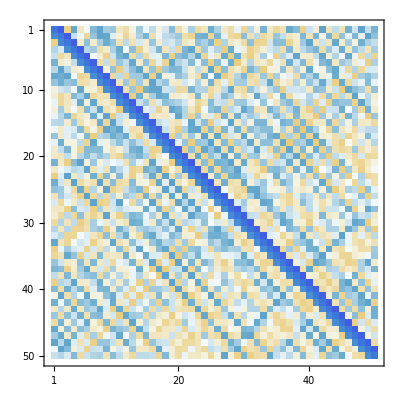

-Graphics3D-

```mathematica
T=ToeplitzMatrix[Take[MPlusBand,ll],Join[{MPlusBand⟦1⟧},Take[MPlusBand,-ll+1]//Reverse]];
use=MMinusAntiBand⟦1;;2*ll-1⟧;
H=HankelMatrix[use⟦1;;ll⟧,(use//RotateLeft[#,-ll]&)⟦1;;ll⟧];
M=(T+H)/(Sqrt[nn]//N[#,prec]&);
S=SingularValueDecomposition[M];
P=(S⟦1⟧^2+S⟦3⟧^2)/2 //N[#,prec]&;
MatrixPlot[M]
ListPlot3D[P,PlotRange->All,ImageSize->Large]
```

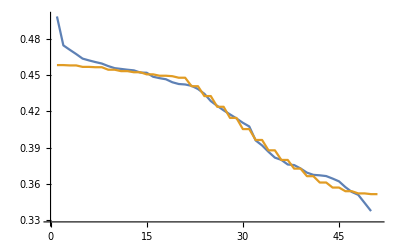

```mathematica
P2[l_]:=1/(Exp[βT (ω[((2 π)/ll) l]-μ)]+1);
A=ReverseSort[Diagonal[-S⟦2⟧+1/2]]//N[#,prec]&;
B=ReverseSort[Table[P2[i],{i,0,ll}]]//N[#,prec]&;
ListLinePlot[{A,B},AxesLabel->Automatic]
```

```mathematica
Σ=(-Diagonal[S⟦2⟧]+1/2//N[#,prec]&);
X=Log[1-Σ]-Log[Σ];
ρT=-((S⟦1⟧.DiagonalMatrix[X].Transpose[S⟦3⟧])/βT);
```

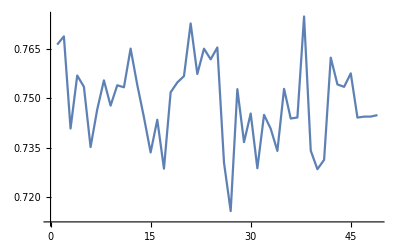

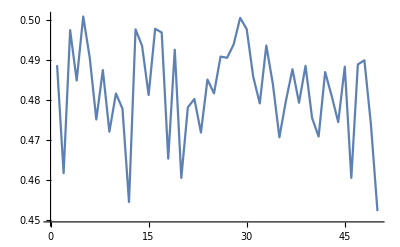

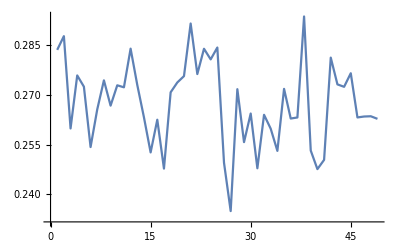

```mathematica
Table[ρT⟦i,i+1⟧, {i,1,ll-1}]//ListLinePlot
Table[ρT⟦i,i⟧, {i,1,ll}]//ListLinePlot
Table[ρT⟦i+1,i⟧, {i,1,ll-1}]//ListLinePlot
```

```mathematica
ListPlot3D[ρT,PlotRange->All,ImageSize->Large]
```

-Graphics3D-

# Averaging over Fourier

```mathematica
nn=80001;
ll=50;
prec=120;
nData=10;
γ=1/2//N[#,prec]&;
λ=1/2//N[#,prec]&;
a0=λ//N[#,prec]&;
a1=(1-γ)/2//N[#,prec]&;
a2=(1+γ)/2//N[#,prec]&;
α[θ_]=(a0+ Cos[θ]);
β[θ_]=(-a1+a2) Sin[θ];
ω[θ_]=Sqrt[α[θ]^2+β[θ]^2];
ϕ[θ_]=ArcTan[α[θ],β[θ]];
t=Table[k,{k,-(nn-1)/2,(nn-1)/2}];
μ=0.0//N[#,prec]&;
βT =0.40824980415756 //N[#,prec]&;
p[l_]:=1/(Exp[βT (ω[((2 π)/nn) l]-μ)]+1);
Timing[(Data = ParallelTable[mCos=Table[If[RandomReal[]>p[k],-(1/2),1/2],{k,1,(nn-1)/2}];
mCos0=If[RandomReal[]>p[0],-(1/2),1/2];
mSin=Table[If[RandomReal[]>p[k],-(1/2),1/2],{k,1,(nn-1)/2}];
mSin0=If[RandomReal[]>p[0],-(1/2),1/2];
(*mCos=Table[-(1/2),{k,1,(nn-1)/2}];
mCos0=-(1/2);
mSin=Table[-(1/2),{k,1,(nn-1)/2}];
mSin0=-(1/2);*)

MPlusBand=((If[#==0,(mCos0+mSin0)/2,(mCos⟦Abs[#]⟧+mSin⟦Abs[#]⟧)/2]) E^(I Sign[(2 π)/nn #] ϕ[Abs[(2 π)/nn #]])&/@t)//RotateLeft[#,(nn-1)/2]&//Fourier;
MMinusAntiBand=((If[#==0,(mCos0-mSin0)/2,(mCos⟦Abs[#]⟧-mSin⟦Abs[#]⟧)/2]) E^(I Sign[(2 π)/nn #] (ϕ[Abs[(2 π)/nn #]]))&/@t)//RotateLeft[#,(nn-1)/2]&//Fourier;
Join[{Join[Take[MPlusBand,ll],Take[MPlusBand,-ll+1]],Take[MMinusAntiBand,2*ll-1]}],{ii,nData}];)]
```

{13.2639,Null}

```mathematica
Export[NotebookDirectory[]<>"Data_Fourier.hdf5",Data,"HDF5"]
```

/Users/josealejandromontanacortes/Documents/Tesis/XY_model/Data_Fourier.hdf5

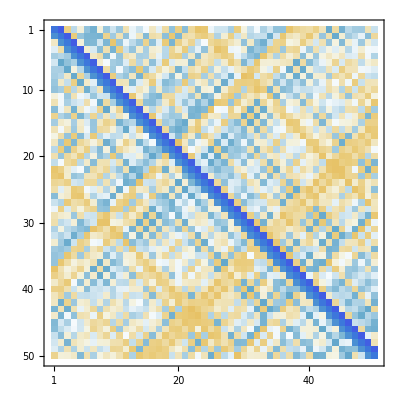

-Graphics3D-

```mathematica
(*Total[Data,{1}]/10;*)
Res=Mean[Data];
T=ToeplitzMatrix[Take[Res⟦1⟧,ll],Join[{Res⟦1⟧⟦1⟧},Take[Res⟦1⟧,-ll+1]//Reverse]];
H= HankelMatrix[Res⟦2⟧⟦1;;ll⟧,(Res⟦2⟧//RotateLeft[#,-ll]&)⟦1;;ll⟧];
M=(T+H)/(Sqrt[nn]//N[#,prec]&);
S=SingularValueDecomposition[M];
P=(S⟦1⟧^2+S⟦3⟧^2)/2 //N[#,prec]&;
MatrixPlot[M]
ListPlot3D[P,PlotRange->All,ImageSize->Large]
```

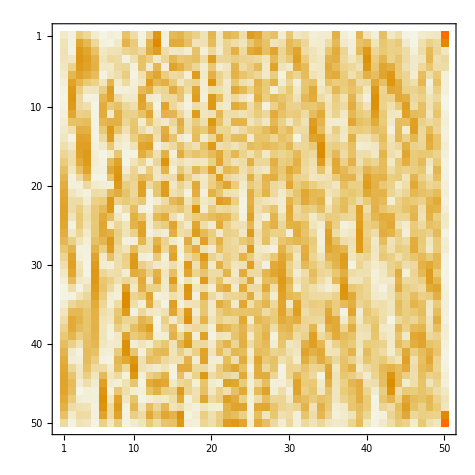

```mathematica
MatrixPlot[P]
```

```mathematica
Export[NotebookDirectory[]<>"Participation.csv",P]
```

/Users/josealejandromontanacortes/Documents/Tesis/XY_model/Participation.csv

```mathematica
Unprotect[$ProcessorCount];$ProcessorCount=8;
```

```mathematica
Print[$ProcessorCount]
```

8

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["Participation.csv"]]]
```

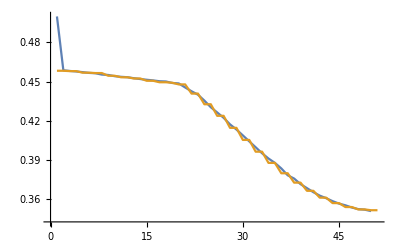

```mathematica
P2[l_]:=1/(Exp[βT (ω[((2 π)/ll) l]-μ)]+1);
A=ReverseSort[Diagonal[-S⟦2⟧+1/2]]//N[#,prec]&;
B=ReverseSort[Table[P2[i],{i,0,ll}]]//N[#,prec]&;
ListLinePlot[{A,B},AxesLabel->Automatic]
```

```mathematica
Σ=(-Diagonal[S⟦2⟧]+1/2//N[#,prec]&);
X=Log[1-Σ]-Log[Σ];
ρT=-((S⟦1⟧.DiagonalMatrix[X].Transpose[S⟦3⟧])/βT);
```

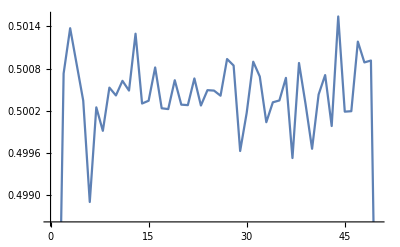
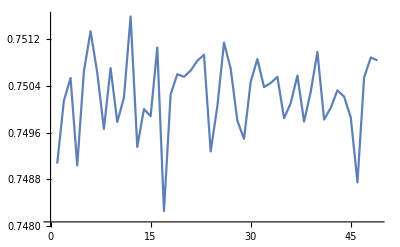
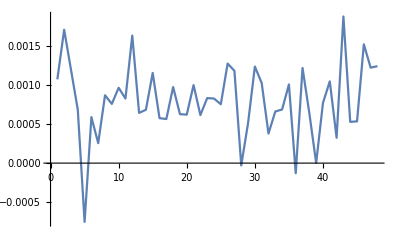
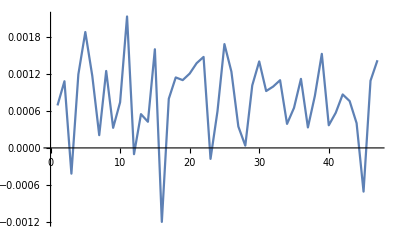
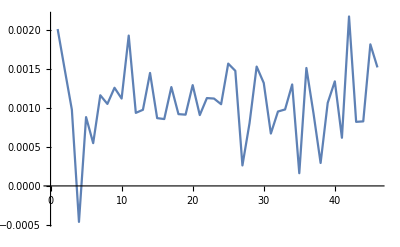
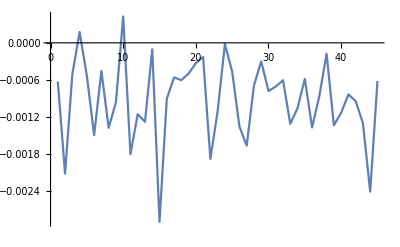
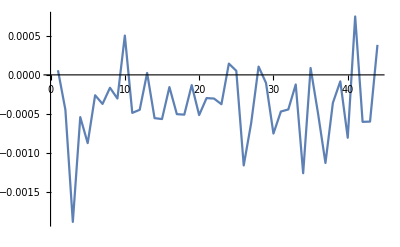
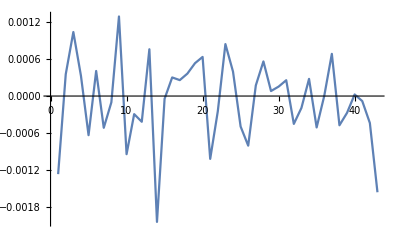

```mathematica
Table[ListLinePlot[Table[ρT⟦i,i+j⟧, {i,1,ll-j}]],{j,0,20}]
```

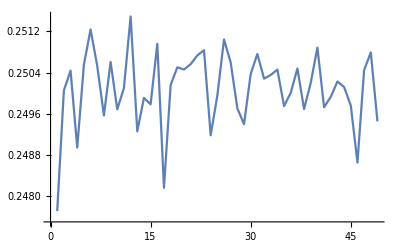
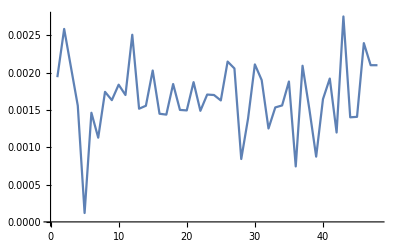
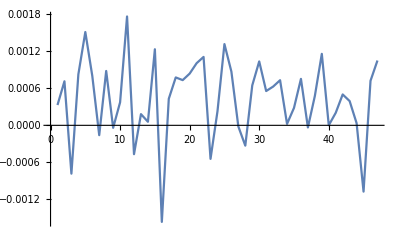
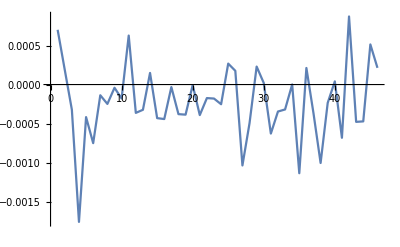
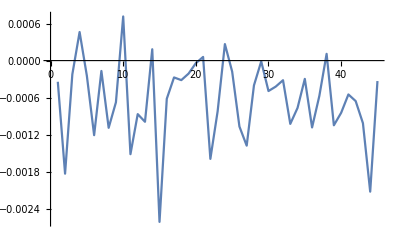
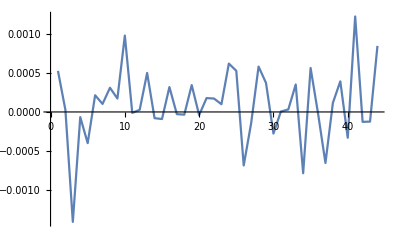
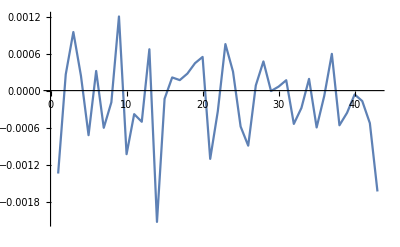
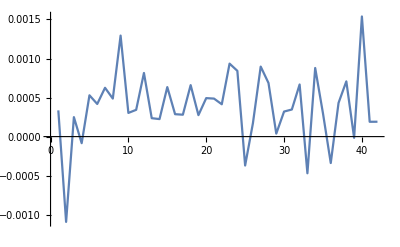
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[ListLinePlot[Table[ρT⟦i+j,i⟧, {i,1,ll-j}]],{j,0,20}]
```